# Wigner Function Reconstruction

## Last Updated: 2025/05/31

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

## FFT-Related

```mathematica
(*recenter a 2D matrix after fourier transform*)
RecenterFourier[data_List]:=RotateRight[
data,
{#1,#2}
][[;;#1*2,;;#2*2]]&@@Floor[Dimensions[data]/2];
```

```mathematica
(*chop off a 2D matrix a lá w/RecenterFourier, but without rotation*)
CutoffGrid[data_List]:=data[[;;#1*2,;;#2*2]]&@@Floor[Dimensions[data]/2];
```

## Image Creation

```mathematica
(*create color scaling for χ(β) plot*)
colorFuncName="DefaultColorFunction"/.(Method/.Charting`ResolvePlotTheme[Automatic,ListDensityPlot]);
colorFunc=ColorData[colorFuncName]@Rescale[#,{-1.,1.},{0.,1.0}]&;
(*create corresponding bar legend*)
colorLegend=BarLegend[{colorFunc,{-1.,1.}}];
```

```mathematica
(*alternate color scaling for χ(β) plot*)
colorFuncName="TemperatureMap";
colorFunc=ColorData[colorFuncName]@Rescale[#-0.,{-1.,1.}/1.,{0.,1.0}]&;
(*create corresponding bar legend*)
colorLegend=BarLegend[{colorFunc,{-1.,1.}}];
```

## ListDensityPlot (2D) - Convenience

```mathematica
(*ListDensityPlot convenience function*)
Remove[Plot2DResults];

(*specify optional arguments and their default value for Plot2D function*)
Options[Plot2DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35]
(*"ImageScale"->0.35*)
(*"args"->None*)
};

(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot2DResults[data_List,OptionsPattern[{Options[Plot2DResults],ListDensityPlot}]]:=Block[
{
(*expand some keyword arguments for convenience*)
AxesLabelVals=OptionValue["AxesLabels"],

(*support 2D flat list of values, or 3D image-type value*)
dataRangeDJ=If[Length[Dimensions[data]]==3,
{MinMax[#[[;;,1]]],MinMax[#[[;;,2]]]}&@(Flatten[data[[;;,;;,;;2]],1]),
Automatic
],
dataPlotDJ=If[Length[Dimensions[data]]==3,
data[[;;,;;,3]],
data
]
},

(*create listdensityplot*)
ListDensityPlot[
dataPlotDJ,

(*plot ranges*)
PlotRange->{
{Full,Full},
{Full,Full},
{-1.0,1.0}
},
DataRange->dataRangeDJ,

(*plotting options*)
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->0,
Mesh->None,
PlotLegends->Placed[colorLegend,Bottom],

(*plot layout*)
FrameLabel->{ 
{Style[AxesLabelVals[[1,1]],{Black,Directive[18]}],None},
{
Style[AxesLabelVals[[2,1]],{Black,Directive[18]}],
Style[AxesLabelVals[[3,1]],{Black,Directive[15]}]
}
},
AspectRatio->0.9,
(*ImageSize->{450,450}*)
(*ImageSize->Scaled[0.25]*)
ImageSize->OptionValue["ImageSize"]
]
];
```

## ListPlot3D (3D) - Convenience

```mathematica
(*ListPlot3D convenience function*)
Remove[Plot3DResults];

(*specify optional arguments and their default value for Plot2D function*)
Options[Plot3DResults]={
(*{{title_label},{x_label},{y_label}}*)
"AxesLabels"->{{""},{""},{""}},
"ImageSize"->Scaled[0.35]
(*"args"->None*)
};

(*Plot2DResults[data_List,args___:None,OptionsPattern[]]:=Block[*)
Plot3DResults[data_List,OptionsPattern[{Options[Plot3DResults],ListDensityPlot}]]:=Block[
{
(*expand some keyword arguments for convenience*)
AxesLabelVals=OptionValue["AxesLabels"]
},

(*create 3D plot*)
ListPlot3D[
data,
PlotLegends->Placed[colorLegend,Bottom],
PlotRange->{
{Full,Full},
{Full,Full},
{-1.0,1.0}
},
ColorFunction->colorFunc,
ColorFunctionScaling->False,
InterpolationOrder->2,
Mesh->None,
(*FrameLabel->{ 
{Style[AxesLabelVals[[1,1]],{Black,Directive[18]}],None},
{
Style[AxesLabelVals[[2,1]],{Black,Directive[18]}],
Style[AxesLabelVals[[3,1]],{Black,Directive[15]}]
}
},*)
AspectRatio->0.9,
(*ImageSize->{450,450}*)
ImageSize->OptionValue["ImageSize"]
(*
(*pass all function arguments down to ListDensityPlot*)
args*)
]
];
```

# User Input

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2025-05\\2025-05-31";
(*directoryString="/Users/claytonho/Documents/Research/Data & Analysis/Motional/Wigner/wigner_data";*)
```

```mathematica
(*list of RIDs to analyze*)
ridList={117478};
```

## Configuration Values

```mathematica
(*convert time to displacement*)
α0={50.,(√2.536)/(0.445018*0.979688)};
```

```mathematica
(*dataset columns - general style*)
countCol=2;
heraldCol=-1;
timeCol=4;
phaseCol=5;
axisCol=6;
```

```mathematica
(*dataset columns - superduperresolution characteristic function*)
countCol=2;
heraldCol=2;
timeCol=3;
phaseCol=4;
axisCol=1;
```

# Import & Preprocess

## Batch Import

```mathematica
(*batch import*)
AbsoluteTiming[
datafileList=ImportDatasetARTIQ[
directoryString,
ToString[#]
]&/@ridList;
]
```

{0.400232,Null}

```mathematica
(*combine all datasets for value check*)
dataset=Join@@datafileList[[;;,1]];
```

```mathematica
(*separate datasets by real vs imag*)
datasetsSorted=GroupBy[dataset,#[[axisCol]]&];
datasetReal=datasetsSorted[0.];
datasetImag=datasetsSorted[1.];
```

```mathematica
(*set parameters as simply the first dataset's*)
parameters=(First@datafileList)[[2]];
```

## Verify Data

```mathematica
(*ListLinePlot[dataset[[#1;;#2,2]],PlotRange->Full]&[
IntegerPart[0.9951*Length[dataset]],
IntegerPart[0.996*Length[dataset]]
]*)
```

```mathematica
(*(*remove bad data*)
th0=dataset;
tha1=dataset[[;;IntegerPart[0.844*Length[dataset]]]];
tha2=dataset[[IntegerPart[0.8924*Length[dataset]];;]];
dataset=Join[tha1,tha2];*)
```

```mathematica
(*dataset=dataset[[;;IntegerPart[0.9952*Length[dataset]]]];*)
```

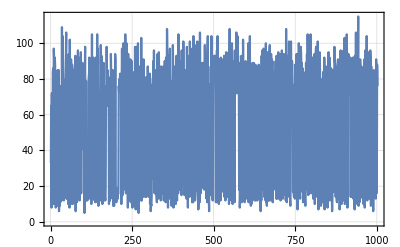
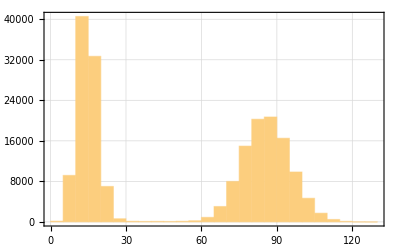
{(0. | 33. | 38180. | 61026.
1. | 19. | 27194. | 34827.
0. | 12. | 33413. | 37976.),-Graphics-,-Graphics-}

```mathematica
(*value check*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;;;Min[Round[Length[#]/1000],1000]]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,countCol]]]
```

```mathematica
(*extract important parameters*)
attCatDB=First@parameters["atts_cat_db"];
amplCatPCT=First@parameters["ampls_cat_pct"];
```

# χ(β) (Characteristic Function) Process

## Process

## Preprocess

```mathematica
(*select heralded if we enable herald*)
(*{datasetProcessedReal,datasetProcessedImag}={datasetReal,datasetImag};*)
{datasetProcessedReal,datasetProcessedImag}={datasetReal,datasetImag};
```

```mathematica
(*threshold dataset counts into P_↓*)
{datasetProcessedReal,datasetProcessedImag}=ThresholdCounts[
#[[;;,{timeCol,phaseCol,countCol}]],
3
]&/@{datasetProcessedReal,datasetImag};
```

```mathematica
(*coarse collate - group data by {r,θ} to reduce processing overhead*)
{datasetProcessedReal,datasetProcessedImag}=CollateData[
#,
{1,2}
]&/@{datasetProcessedReal,datasetProcessedImag};
(*flatten back into a list*)
{datasetProcessedReal,datasetProcessedImag}=Flatten[Values@Values@#,1]&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*convert {r,θ} values from machine units to relevant units*)
{datasetProcessedReal,datasetProcessedImag}=Transpose[
Transpose[#]*{(1.*^-3),1./(2^16-1.),1.}(*t_ns->t_μs, pow->turns, counts*)
]&/@{datasetProcessedReal,datasetProcessedImag};
(*convert P_↓ to ⟨χ(β)⟩*)
datasetProcessedReal[[;;,3]]=2.*datasetProcessedReal[[;;,3]]-1.;
datasetProcessedImag[[;;,3]]=2.*datasetProcessedImag[[;;,3]]-1.;
```

## Convert To Grid

```mathematica
(*convert {r,θ} to {x,y}*)
{dsXYtmpReal,dsXYtmpImag}=(#[[;;,1]]*Exp[ⅈ*(2.π)*(#[[;;,2]]-0.)]*α0[[2]]/α0[[1]])&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*ensure x,y values are correctly rounded to ensure grid is regular*)
{xValsTMPReal,yValsTMPReal,xValsTMPImag,yValsTMPImag}=Round[#,(Max[#]-Min[#])/Length[#]*2.]&/@{Re[dsXYtmpReal],Im[dsXYtmpReal],Re[dsXYtmpImag],Im[dsXYtmpImag]};
datasetProcessedReal[[;;,{1,2}]]=Transpose[{xValsTMPReal,yValsTMPReal}];
datasetProcessedImag[[;;,{1,2}]]=Transpose[{xValsTMPImag,yValsTMPImag}];
```

```mathematica
(*confirm gridded correctly*)
Dimensions/@(DeleteDuplicates/@{xValsTMPReal,yValsTMPReal})
Dimensions/@(DeleteDuplicates/@{xValsTMPImag,yValsTMPImag})
```

{{31},{31}}

{{31},{31}}

## Prepare for Display

```mathematica
(*group datasets by x, then y, to form a 2D grid*)
{datasetProcessedReal,datasetProcessedImag}=CollateData[
#,
{1,2}
]&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*sort data correctly*)
{datasetProcessedReal,datasetProcessedImag}=KeySort/@#&/@(KeySort/@{datasetProcessedReal,datasetProcessedImag});
{datasetProcessedReal,datasetProcessedImag}=(Values@Values@#)&/@{datasetProcessedReal,datasetProcessedImag};
```

```mathematica
(*(*tmp remove - intercept*)
(*{dsCharRe,dsCharIm}={datasetProcessedReal,datasetProcessedImag};*)
{dsOGRe,dsOGIm}={datasetProcessedReal,datasetProcessedImag};
{datasetProcessedReal,datasetProcessedImag}={fitDataPlotRe,fitDataPlotIm};
(*tmp remove - intercept*)*)
```

```mathematica
(*gridRange={-3.,3.,0.2};gridDisplace=2.*Exp[2.π*ⅈ*0.0];filtKern=10;
gridVals=Table[{x,y,0},{x,gridRange[[1]],gridRange[[2]],gridRange[[3]]},{y,gridRange[[1]],gridRange[[2]],gridRange[[3]]}];
gridVals[[;;,;;,3]]=Apply[χCoherent[##,gridDisplace]&,gridVals[[;;,;;,;;2]],{2}]//Re;
(*gridVals[[;;,;;,3]]=GaussianFilter[gridVals[[;;,;;,3]],filtKern];*)
datasetProcessedReal=gridVals;
gridVals=Table[{x,y,0},{x,gridRange[[1]],gridRange[[2]],gridRange[[3]]},{y,gridRange[[1]],gridRange[[2]],gridRange[[3]]}];
gridVals[[;;,;;,3]]=Apply[χCoherent[##,gridDisplace]&,gridVals[[;;,;;,;;2]],{2}]//Im;
(*gridVals[[;;,;;,3]]=GaussianFilter[gridVals[[;;,;;,3]],filtKern];*)
datasetProcessedImag=gridVals;
{Plot2DResults[Flatten[datasetProcessedReal,1]],Plot2DResults[Flatten[datasetProcessedImag,1]]}*)
```

```mathematica
(*store grid-ed dataset before flattening for display*)
{dsCharRe,dsCharIm}={datasetProcessedReal,datasetProcessedImag};
{datasetProcessedReal,datasetProcessedImag}=Flatten[#,1]&/@{datasetProcessedReal,datasetProcessedImag};
(*{datasetProcessedReal,datasetProcessedImag}=Flatten[#,1]&/@{fitDataPlotRe,fitDataPlotIm};*)
```

```mathematica
dsCharIm//Dimensions
```

{31,31,3}

## Summary Statistics

```mathematica
{charReMax,charImMax}=Max/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReMin,charImMin}=Min/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReAvg,charImAvg}=Mean/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
{charReStd,charImStd}=StandardDeviation/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}
```

{0.86,0.92}

{-1.,-0.96}

{-0.0660562,-0.0547138}

{0.348565,0.352657}

## Plot

```mathematica
(*plot χ(β) separately for Re[χ(β)] and Im[χ(β)]*)
{dsChi3DPlotReal,dsChi3DPlotImag}=MapThread[
Plot2DResults[
#1,
AxesLabels->{{"Im[β]"},{"Re[β]"},{"Raw Data - "<>#2<>"\nRID(s): "<>ToString[ridList]}},
ImageSize->Scaled[0.29]
]&,
{
(*{datasetProcessedReal,datasetProcessedImag},*)
{dsCharRe,dsCharIm},
{"Re[χ(β)]","Im[χ(β)]"}
}
];
```

## Show

```mathematica
(*{Mean[datasetProcessedImag[[;;,3]]],parameters["time_superresolution_stop_us"],parameters["phase_characteristic_axis_turns"]}
{MinMax[datasetProcessedReal[[;;,3]]],MinMax[datasetProcessedImag[[;;,3]]]}
{dsChi3DPlotReal,dsChi3DPlotImag}*)
```

# χ(β) Fitting

## Fit Parameters

## Fit Parameters - Ground State

```mathematica
(*guess fit parameters for χ(β) - ground state*)
fitGuessParams={
0.5,(*wavepacket extent - σ*)
0.9,(*amplitude*)
0.1(*bias/offset*)
};

(*specify additional fit constraints*)
fitCharConstraints={
ampl==1.-bias
};

(*fit function to use for χ(β) - ground state*)
fitCharFunc={FitCharacteristicGroundRe,FitCharacteristicGroundIm};
```

## Fit Parameters - Coherent State

```mathematica
(*guess fit parameters for χ(β) - coherent state*)
fitGuessParams={
Re[#1*Exp[ⅈ*(2.π)*#2]],(*complex displacement*)
Im[#1*Exp[ⅈ*(2.π)*#2]],(*complex displacement*)
1.,(*wavepacket spread*)
0.95,(*χ amplitude*)
0.05(*bias/offset*)
}&[3.1,-0.5](*|α|, Arg[α]*);

(*specify additional fit constraints*)
fitCharConstraints={
ampl==1.-bias
(*σ==1.*)
};

(*fit function to use for χ(β) - coherent state*)
fitCharFunc={FitCharacteristicCoherentRe,FitCharacteristicCoherentIm};
```

## Functions

```mathematica
(*squeezed: β*Cosh[r]+Conjugate[β]*Exp[ⅈ*θ]*Sinh[r]  *)
```

## Ground State

```mathematica
(*characteristic function for the ground state*)
χGround[x_,y_,σ_:1.]:=-Exp[(-(x^2.+y^2.))/(2. σ^2.)];
```

```mathematica
(*fit characteristic function: ground state - real*)
FitCharacteristicGroundRe[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,σ,ampl,bias,(*fit parameters*)
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.}
]
},
Return[
NonlinearModelFit[
data,
Join[
(*{(-Exp[(-(x^2.+y^2.))/(2. σ^2.)])*ampl+bias},*)
{-1.*(Exp[(-(x^2.+y^2.))/(2. σ^2.)]*(ampl)+bias)},
fitConstraints
],
Transpose[{{σ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

```mathematica
(*fit characteristic function: ground state - imag*)
FitCharacteristicGroundIm[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,σ,ampl,bias,(*fit parameters*)
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.}
]
},
Return[
NonlinearModelFit[
data,
Join[
(*{(-Exp[(-(x^2.+y^2.))/(2. σ^2.)])*ampl+bias},*)
{1.*(Exp[(-(x^2.+y^2.))/(2. σ^2.)]*(ampl)+bias)},
fitConstraints
],
Transpose[{{σ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

## Coherent States

```mathematica
(*characteristic function for a coherent state*)
χCoherent[x_,y_,σ_:1.,α_:0.]:=-Exp[(-(x^2.+y^2.))/(2. σ^2.)]*Exp[2*ⅈ*(y*Re[α]-x*Im[α])];
```

```mathematica
(*fit characteristic function: coherent state - real*)
Clear[FitCharacteristicCoherentRe];
FitCharacteristicCoherentRe[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,
σ,a,b,ampl,bias,
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.,0.,0.}
]
},

Return[
NonlinearModelFit[
data,
Join[
(*{(-Exp[-(x^2.+y^2.)/(2.*σ^2.)]*Cos[2.*(y*a-x*b)])*ampl+bias},*)
{-1.*((Exp[-(x^2.+y^2.)/(2.*σ^2.)]*Cos[2.*(y*a-x*b)])*(ampl)+bias)},
fitConstraints
],
Transpose[{{a,b,σ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

```mathematica
(*fit characteristic function: coherent state - imag*)
Clear[FitCharacteristicCoherentIm];
FitCharacteristicCoherentIm[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,
σ,a,b,ampl,bias,
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.,0.,0.}
]
},

Return[
NonlinearModelFit[
data,
Join[
(*{(-Exp[-(x^2.+y^2.)/(2. σ^2.)]*Sin[2.*(y*a-x*b)])*ampl-bias},*)
{-1.*((Exp[-(x^2.+y^2.)/(2. σ^2.)]*Sin[2.*(y*a-x*b)])*(ampl)-bias)},
fitConstraints
],
Transpose[{{a,b,σ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

## Squeezed States

```mathematica
(*characteristic function for the ground state*)
χSqueezed[x_,y_,σ_:1.,r_:0.,θ_:0.5]:=-Exp[(-(#1^2.+#2^2.))/(2. σ^2.)]&[
Cosh[r]*x+Sinh[r]*(x*Cos[θ]+y*Sin[θ]),(*x - squeezed*)
Cosh[r]*x+Sinh[r]*(x*Sin[θ]-y*Cos[θ])(*y - squeezed*)
];
```

```mathematica
(*fit characteristic function: squeezed state - real*)
FitCharacteristicSqueezedRe[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,
σ,r,θ,ampl,bias,(*fit parameters*)
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.,0.,0.}
]
},
Return[
NonlinearModelFit[
data,
Join[
{(-Exp[(-(x^2.+y^2.))/(2. σ^2.)])*ampl+bias},
fitConstraints
],
Transpose[{{σ,r,θ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

```mathematica
(*fit characteristic function: squeezed state - imag*)
FitCharacteristicSqueezedIm[data_List,fitGuess_List:{},fitConstraints_List:{}]:=Block[
{
x,y,
σ,r,θ,ampl,bias,(*fit parameters*)
guessVals=If[Length[fitGuess]==3,
fitGuess,
{0.,0.,0.,0.,0.}
]
},
Return[
NonlinearModelFit[
data,
Join[
{(-Exp[(-(x^2.+y^2.))/(2. σ^2.)])*ampl+bias},
fitConstraints
],
Transpose[{{σ,r,θ,ampl,bias},fitGuess}],
{x,y}
]
];
];
```

## Cat States

```mathematica
(*characteristic function for a cat state*)
χCat[x_,y_,α_,ϕ_]:=-Exp[-(x^2.+y^2.)/2.]/(2.*(1.+Cos[ϕ]*Exp[-Abs[α]^2./2.]))*(
1.+Exp[2.*ⅈ*(y*Re[α]-x*Im[α])]+Exp[-Abs[α]^2./2.]*(Exp[-ⅈ*ϕ+Conjugate[α]*(x+ⅈ*y)]+Exp[ⅈ*ϕ-α*(x-ⅈ*y)])
);
```

```mathematica
(*todo: fit characteristic function: cat state*)
FitCharacteristicCat[data_List]:=Block[
{x,y,a,b,ampl,bias},
Return[
NonlinearModelFit[
data,
(-Exp[(-(x^2.+y^2.))/2.]*Cos[2.*(y*a-x*b)])*ampl+bias,
{
{a,9.8},
{b,2.7},
{ampl,1.},
{bias,0.}
},
{x,y}
]
];
];
```

## Fock States

## Fit Characteristic Function

## Real

```mathematica
(*fit χ - real*)
AbsoluteTiming[
resDJRe=fitCharFunc[[1]][
Flatten[dsCharRe,1],
fitGuessParams,
fitCharConstraints
];
]
```

{0.0500655,Null}

```mathematica
(*create fit parameter table*)
fitParamsRe=Style[
resDJRe["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*plot fit and compare to data*)
fitDataPlotRe=dsCharRe;
fitDataPlotRe[[;;,;;,3]]=Apply[resDJRe,dsCharRe[[;;,;;,;;2]],{2}];
(*{Plot2DResults[Flatten[dsCharRe,1]],Plot2DResults[Flatten[fitDataPlotRe,1]]}*)
```

## Imaginary

```mathematica
(*fit χ - imag*)
AbsoluteTiming[
resDJIm=fitCharFunc[[2]][
Flatten[dsCharIm,1],
fitGuessParams,
fitCharConstraints
];
]
```

{0.0652258,Null}

```mathematica
(*create fit parameter table*)
fitParamsIm=Style[
resDJIm["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*plot fit on grid*)
fitDataPlotIm=dsCharIm;
fitDataPlotIm[[;;,;;,3]]=Apply[resDJIm,dsCharIm[[;;,;;,;;2]],{2}];
(*{Plot2DResults[Flatten[dsCharIm,1]],Plot2DResults[Flatten[fitDataPlotIm,1]]}*)
```

## Create Analytical

```mathematica
(*gridVals=Table[{x,y,0},{x,-1.5,1.5,0.15},{y,-1.5,1.5,0.15}];
gridVals[[;;,;;,3]]=Apply[χCoherent[##,3.*Exp[2.π*ⅈ*0.03]]&,gridVals[[;;,;;,;;2]],{2}]//Im;
Plot2DResults[Flatten[gridVals,1]]*)
```

## Use Fit to Process Data

```mathematica
(*subtract offset and rescale amplitude - real*)
dsCharFitProcRe=dsCharRe;
dsCharFitProcRe[[;;,;;,3]]=(dsCharFitProcRe[[;;,;;,3]]+#[[2]])/(#[[1]])&[{1.-bias,bias}/.resDJRe["BestFitParameters"]];
```

```mathematica
(*subtract offset and rescale amplitude - imag*)
dsCharFitProcIm=dsCharIm;
dsCharFitProcIm[[;;,;;,3]]=(dsCharFitProcIm[[;;,;;,3]]-#[[2]])/(#[[1]])&[{1.-bias,bias}/.resDJIm["BestFitParameters"]];
```

```mathematica
MinMax/@{datasetProcessedReal[[;;,3]],datasetProcessedImag[[;;,3]]}//Transpose//MatrixForm
MinMax/@{fitDataPlotRe[[;;,;;,3]],fitDataPlotIm[[;;,;;,3]]}//Transpose//MatrixForm
MinMax/@{dsCharFitProcRe[[;;,;;,3]],dsCharFitProcIm[[;;,;;,3]]}//Transpose//MatrixForm
```

(-1. | -0.96
0.86 | 0.92)

(-1. | -1.04535
0.825091 | 0.96002)

(-1. | -0.879796
1.00164 | 0.923274)

## Plot Data

```mathematica
(*plot fitted data*)
AbsoluteTiming[
{dsChiFitPlotReal,dsChiFitPlotImag}=MapThread[
Plot2DResults[
#1,
AxesLabels->{
{"Im[β]"},
{"Re[β]"},
{"Fitted - "<>#2<>"\nRID(s): "<>ToString[ridList]}
},
ImageSize->Scaled[0.28]
]&,
{
{fitDataPlotRe,fitDataPlotIm},
{"Re[χ(β)]","Im[χ(β)]"}
}
];
]
```

{0.0875808,Null}

```mathematica
(*plot renormalized data*)
AbsoluteTiming[
{dsChiFitProcPlotReal,dsChiFitProcPlotImag}=MapThread[
Plot2DResults[
#1,
AxesLabels->{
{"Im[β]"},
{"Re[β]"},
{"Normalized - "<>#2<>"\nRID(s): "<>ToString[ridList]}
},
ImageSize->Scaled[0.28]
]&,
{
{dsCharFitProcRe,dsCharFitProcIm},
{"Re[χ(β)]","Im[χ(β)]"}
}
];
]
```

{0.0765349,Null}

# χ(β) Show

```mathematica
(*dsCharRe=dsCharFitProcRe;
dsCharIm=dsCharFitProcIm;*)
```

```mathematica
(*{{Sqrt[a^2.+b^2.],Arg[a+ⅈ*b]/π}/.resDJRe["BestFitParameters"],
{Sqrt[a^2.+b^2.],Arg[a+ⅈ*b]/π}/.resDJIm["BestFitParameters"]}//MatrixForm
fitParamsRe
fitParamsIm*)
```

```mathematica
(*{
{dsChi3DPlotReal,{fitParamsRe,dsChiFitPlotReal}//MatrixForm,dsChiFitProcPlotReal},
{dsChi3DPlotImag,{fitParamsIm,dsChiFitPlotImag}//MatrixForm,dsChiFitProcPlotImag}
}
{{fitParamsRe,dsChiFitPlotReal}//MatrixForm,{fitParamsIm,dsChiFitPlotImag}//MatrixForm}*)
```

# Wigner Function Reconstruction

```mathematica
{dsCharRe//Dimensions,dsCharIm//Dimensions}
(*Dimensions/@(DeleteDuplicates/@{xValsTMPReal,yValsTMPReal})
Dimensions/@(DeleteDuplicates/@{xValsTMPImag,yValsTMPImag})*)
```

{{31,31,3},{31,31,3}}

```mathematica
(*number of zero-values to pad matrix in EACH direction*)
numZeroPad=50;
(*total grid length to extend via resampling*)
numResampleExtend=0;
```

## Preprocess for FFT

## Resample/Interpolate Onto Identical Square Grid

### Real Part

```mathematica
(*real value dimensions*)
xDimResample=Max[Length[dsCharRe[[;;,1,1]]],numResampleExtend];
yDimResample=Max[Length[dsCharRe[[1,;;,2]]],numResampleExtend];
```

```mathematica
(*interpolate results - real*)
dsCharRe2=Transpose[
Table[
ArrayResample[
dsCharRe[[;;,;;,i]],
{xDimResample,yDimResample}
],
{i,3}
],
{3,1,2}
(*{3,2,1}*)
];
```

### Imaginary Part

```mathematica
(*imag value dimensions*)
xDimResample=Max[Length[dsCharIm[[;;,1,1]]],numResampleExtend];
yDimResample=Max[Length[dsCharIm[[1,;;,2]]],numResampleExtend];
```

```mathematica
(*interpolate results - imag*)
dsCharIm2=Transpose[
Table[
ArrayResample[
dsCharIm[[;;,;;,i]],
{xDimResample,yDimResample}
],
{i,3}
],
{3,1,2}
(*{3,2,1}*)
];
```

```mathematica
(*(*tmp remove-rotate*)
dsCharIm2[[;;,;;,3]]=Reverse[dsCharIm2[[;;,;;,3]],1];
(*tmp remove-rotate*)*)
```

## Zero-Pad & Rescale Axes

### Real Part

```mathematica
(*zero pad grid results*)
dsCharReWigner=Transpose[
(*ArrayPad[#,numZeroPad]&/@Transpose[dsCharRe,3<->1],*)
ArrayPad[#,numZeroPad]&/@Transpose[dsCharRe2,3<->1],
3<->1
];
(*get dimensions of the axes*)
lengthXDim=Length[dsCharReWigner[[;;,1,1]]];
lengthYDim=Length[dsCharReWigner[[1,;;,2]]];
```

```mathematica
(*extend x-axes correctly*)
gridXVals=dsCharReWigner[[numZeroPad+1;;-(numZeroPad+1),numZeroPad+1,1]];
grixXidx=Range[lengthXDim][[numZeroPad+1;;-(numZeroPad+1)]];
AbsoluteTiming[
gridXFit=LinearModelFit[
Transpose[{grixXidx,gridXVals}],
{1,x},
x
];
]
```

{0.0010873,Null}

```mathematica
AbsoluteTiming[
Do[
dsCharReWigner[[i,;;,1]]=gridXFit[#]&/@Range[lengthXDim]//Chop,
{i,lengthXDim}
];
]
```

{0.416683,Null}

```mathematica
(*extend y-axes correctly*)
gridYVals=dsCharReWigner[[numZeroPad+1,numZeroPad+1;;-(numZeroPad+1),2]];
grixYidx=Range[lengthYDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridYFit=LinearModelFit[
Transpose[{grixYidx,gridYVals}],
{1,y},
y
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharReWigner[[;;,i,2]]=gridYFit[#]&/@Range[lengthYDim]//Chop,
{i,lengthYDim}
];
]
```

{0.413472,Null}

```mathematica
(*save processed axes/grid for characteristic before we rescale*)
dsGridCharRe=dsCharReWigner[[;;,;;,;;2]];
(*calculate axes rescaling for wigner - real - x and y*)
dsCharReWigner[[;;,;;,1]]*=1.*π/(lengthXDim*(gridXFit["BestFitParameters"][[2]])^2);
dsCharReWigner[[;;,;;,2]]*=1.*π/(lengthYDim*(gridYFit["BestFitParameters"][[2]])^2);
```

### Imaginary Part

```mathematica
(*zero pad grid results*)
dsCharImWigner=Transpose[
(*ArrayPad[#,numZeroPad]&/@Transpose[dsCharIm,3<->1],*)
ArrayPad[#,numZeroPad]&/@Transpose[dsCharIm2,3<->1],
3<->1
];
(*get dimensions of the axes*)
lengthXDim=Length[dsCharImWigner[[;;,1,1]]];
lengthYDim=Length[dsCharImWigner[[1,;;,2]]];
```

```mathematica
(*extend x-axes correctly*)
gridXVals=dsCharImWigner[[numZeroPad+1;;-(numZeroPad+1),numZeroPad+1,1]];
grixXidx=Range[lengthXDim][[numZeroPad+1;;-(numZeroPad+1)]];
AbsoluteTiming[
gridXFit=LinearModelFit[
Transpose[{grixXidx,gridXVals}],
{1,x},
x
];
]
```

{0.0010195,Null}

```mathematica
AbsoluteTiming[
Do[
dsCharImWigner[[i,;;,1]]=gridXFit[#]&/@Range[lengthXDim]//Chop,
{i,lengthXDim}
];
]
```

{0.41828,Null}

```mathematica
(*extend y-axes correctly*)
gridYVals=dsCharImWigner[[numZeroPad+1,numZeroPad+1;;-(numZeroPad+1),2]];
grixYidx=Range[lengthYDim][[numZeroPad+1;;-(numZeroPad+1)]];
gridYFit=LinearModelFit[
Transpose[{grixYidx,gridYVals}],
{1,y},
y
];
```

```mathematica
AbsoluteTiming[
Do[
dsCharImWigner[[;;,i,2]]=gridYFit[#]&/@Range[lengthYDim]//Chop,
{i,lengthYDim}
];
]
```

{0.406316,Null}

```mathematica
(*save processed axes/grid for characteristic before we rescale*)
dsGridCharRe=dsCharImWigner[[;;,;;,;;2]];
(*calculate axes rescaling for wigner - imag - x and y*)
dsCharImWigner[[;;,;;,1]]*=1.*π/(lengthXDim*(gridXFit["BestFitParameters"][[2]])^2.);
dsCharImWigner[[;;,;;,2]]*=1.*π/(lengthYDim*(gridYFit["BestFitParameters"][[2]])^2.);
```

## 2D FFT for Wigner

```mathematica
(*(*use convolution trick to recenter correctly*)
rotMat=-Table[(-1)^(-1+i+j),{i,#1},{j,#2}]&@@Dimensions[dsCharReWigner];*)
```

```mathematica
(*prepare calculation of fourier matrices*)
βx=dsGridCharRe[[1,;;,1]];βy=dsGridCharRe[[;;,1,2]];
γx=dsCharReWigner[[1,;;,1]];γy=dsCharReWigner[[;;,1,2]];
(*create manual fourier matrices*)
Mki=Exp[2.*ⅈ*KroneckerProduct[γy,βx]];
Fjl=Exp[-2.*ⅈ*KroneckerProduct[βy,γx]];
```

```mathematica
(*condense Re[χ] and Im[χ] into χij*)
χij=dsCharReWigner[[;;,;;,3]]-ⅈ*dsCharImWigner[[;;,;;,3]];
```

```mathematica
(*do manual, characteristic-special, 2D FFT!*)
AbsoluteTiming[
wignerValsTMP=-Mki.(χij(**rotMat*)).Fjl;
]
```

{0.0003974,Null}

```mathematica
(*scale by (Subscript[Δβ, x] Subscript[Δβ, y])/π^2 per fluhmann-ish*)
wignerValsTMP*=2./π^2.*(gridXFit["BestFitParameters"][[2]]*gridYFit["BestFitParameters"][[2]]);
(*fudge factor for scaling wrt zero-padding*)
wignerValsTMP/=(1.+numZeroPad/lengthXDim)*1.;
wignerValsTMP/=Max[Abs[wignerValsTMP]];
```

```mathematica
MinMax[Flatten[Re[wignerValsTMP]]]
```

{-0.140434,0.960876}

```mathematica
(*prepare wigner result for plotting*)
dsWigner=dsCharReWigner;
dsWigner[[;;,;;,3]]=Transpose[wignerValsTMP];
```

## Plot

```mathematica
(*create listdensityplot data*)
dsWignerPlotDataReal=dsWigner;
dsWignerPlotDataImag=dsWigner;
dsWignerPlotDataAbs=dsWigner;
dsWignerPlotDataArg=dsWigner;
dsWignerPlotDataReal[[;;,;;,3]]=Re[dsWignerPlotDataReal[[;;,;;,3]]];
dsWignerPlotDataImag[[;;,;;,3]]=Im[dsWignerPlotDataImag[[;;,;;,3]]];
dsWignerPlotDataAbs[[;;,;;,3]]=Abs[dsWignerPlotDataAbs[[;;,;;,3]]];
dsWignerPlotDataArg[[;;,;;,3]]=Arg[dsWignerPlotDataArg[[;;,;;,3]]]/π;
```

```mathematica
(*create text string*)
titleString=""<>IntegerPart[Round[parameters["time_superresolution_stop_us"]]]
```

StringJoin::string: String expected at position 1 in StringJoin[600].

StringJoin[600]

```mathematica
(*plot Wigner*)
AbsoluteTiming[
{dsWignerAbs3DPlot,dsWignerArg3DPlot,dsWignerRe3DPlot,dsWignerIm3DPlot}=
MapThread[
Plot2DResults[
#1,
AxesLabels->{{"Im[γ]"},{"Re[γ]"},{"Wigner Reconstruction - "<>#2<>"\nRID(s): "<>ToString[ridList]}},
ImageSize->Scaled[0.31]
]&,
{
{dsWignerPlotDataAbs,dsWignerPlotDataArg,dsWignerPlotDataReal,dsWignerPlotDataImag},
{"Abs[W(γ)]","Arg[W(γ)]","Re[W(γ)]","Im[W(γ)]"}
}
];
]
```

{1.67675,Null}

## Show

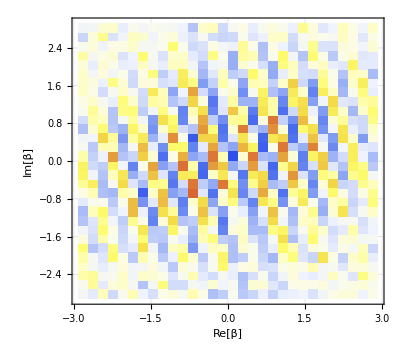
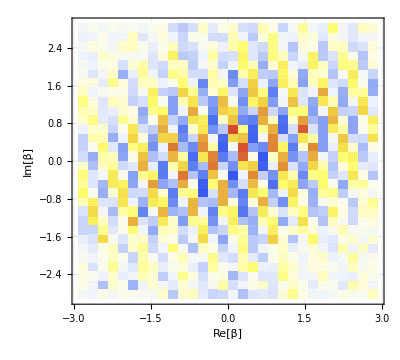

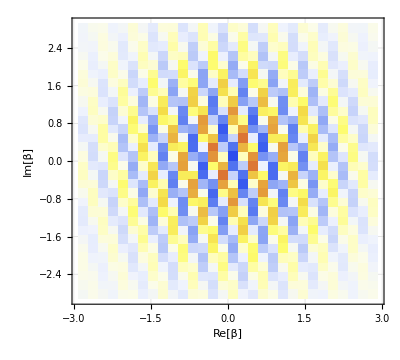
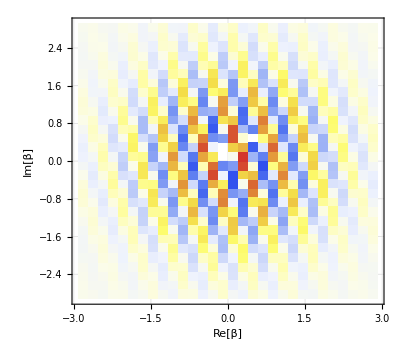
{( | Estimate | Standard Error | Confidence Interval
a | -4.66097 | 0.00667165 | {-4.67406,-4.64787}
b | 1.58796 | 0.0066716 | {1.57487,1.60105}
σ | 1.70892 | 0.0320593 | {1.64601,1.77184}
ampl | 0.929236 | 0.0213689 | {0.887301,0.971171}
bias | 0.0707638 | 0.00501325 | {0.0609256,0.0806021}
-Graphics-),( | Estimate | Standard Error | Confidence Interval
a | -4.66527 | 0.0110083 | {-4.68688,-4.64367}
b | 1.54725 | 0.0110083 | {1.52565,1.56886}
σ | -1.47081 | 0.0361712 | {-1.54179,-1.39982}
ampl | 1.04267 | 0.0341111 | {0.975725,1.10961}
bias | -0.0426662 | 0.00714189 | {-0.0566818,-0.0286506}
-Graphics-)}

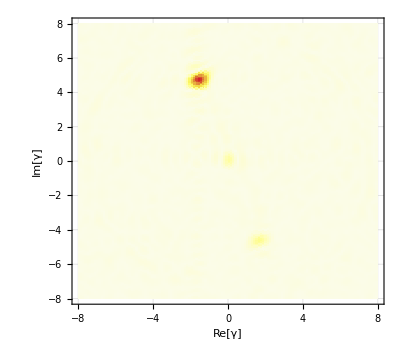
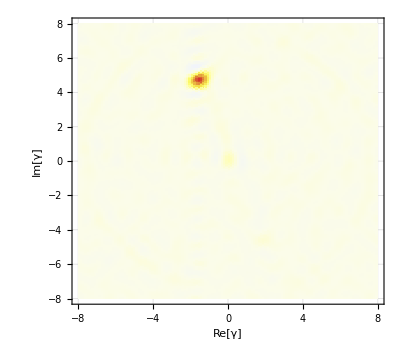
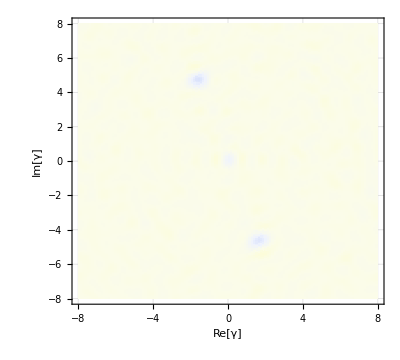

```mathematica
{dsChi3DPlotReal,dsChi3DPlotImag}
{{fitParamsRe,dsChiFitPlotReal}//MatrixForm,{fitParamsIm,dsChiFitPlotImag}//MatrixForm}
{dsWignerAbs3DPlot,(*dsWignerArg3DPlot,*)dsWignerRe3DPlot,dsWignerIm3DPlot}
```

## Show Sexier

```mathematica
(*get waveform time from title*)
waveformTimeUS=If[parameters["enable_phaser"]==0,
0.,
If[parameters["enable_cutoff"]==0,
parameters["time_eggs_heating_us"],
parameters["time_superresolution_stop_us"]
]
];
(*create text string*)
titleString="Elapsed Time: "<>ToString[IntegerPart[Round[waveformTimeUS]]]<>" us";
```

```mathematica
Plot2DResults[
dsWignerPlotDataReal,
AxesLabels->{{"Im[γ]"},{"Re[γ]"},{"Wigner Reconstruction - SuperResolution Trajectory"<>"\n"<>titleString}},
ImageSize->Scaled[0.31]
]
```

-Graphics-

# Kino Wigner

```mathematica
(*(*GIF creation config*)
directoryKino="Z:\\motion\\Data\\2025-05\\wigner_2025_05_30_sdr_ip_biggest_200Hz_both\\";
exportName="wigner_2025_05_30_sdr_ip_biggest_200Hz_both.gif";
normalizedFrameTime=2.5;*)
```

## Import

```mathematica
(*(*import constituent frames and get their groupstring*)
kinoFileStr=FileNames[{"*.png"},directoryKino];
kinoProcStr=ToExpression[
StringExtract[
#,
FileNameSplit[directoryKino][[-1]]<>"\\"->2,
"us"->1
]&/@kinoFileStr
];*)
```

## Process & Export

```mathematica
(*(*sort images by groupstring*)
kinoImages=AssociationThread[kinoProcStr,Import[#]&/@kinoFileStr]//KeySort;
(*set image times by groupstring distances*)
imgTimes=normalizedFrameTime*((#[[2;;-1]]-#[[1;;-2]])/Max[#[[2;;-1]]-#[[1;;-2]]])&[Keys[kinoImages]];
imgTimes=Join[imgTimes,{2*normalizedFrameTime}];*)
```

```mathematica
(*(*create GIF and export*)
kinoGIF=Export[
FileNameJoin[{directoryKino,exportName}],
Values[kinoImages],
"GIF",
"DisplayDurations"->imgTimes
];*)
```